```mathematica
(*Производная от скалярного потенциала ЛВ
$$\varphi=\frac{q}{r-\vec{v}\cdot\vec{r}/c}$$
легко рассчитывается
$$\frac{\partial\varphi}{\partial t}=q\frac{(r/c)(v^2-\vec{w}\cdot\vec{r})-\vec{v}\cdot\vec{r}}{(r-\vec{v}\cdot\vec{r}/c)^3},$$
причем все величины в правой части формулы должны быть взяты в запаздывающий момент $t'$ ($\vec{w}$-ускорение заряда).Понятно,что при расчетах $r$ можно заменить на $c(t-t')$.Скалярные произведения в силу прямолинейного движения вдоль оси $x$ меняются на $v(t')(x-s(t'))$ и $w(t')(x-s(t'))$.Ну а ускорение присутствует и постоянно только при разгоне. Поэтому кодируется строкой
w[t_]:=If[t<0,0,If[t<t0,a,0]];
С уважением.
В полученном выражении для производной проворонил общий знак минус.Правильно
$$\frac{\partial\varphi}{\partial t}=-q\frac{(r/c)(v^2-\vec{w}\cdot\vec{r})-\vec{v}\cdot\vec{r}}{(r-\vec{v}\cdot\vec{r}/c)^3}.$$
С уважением.*)


vk=0.5; (* конечная скорость *)
```

```mathematica
a= 0.1; (* ускорение *)
```

```mathematica
epsilon = 10^(-10); (* погрешность *)
```

```mathematica
t0=vk/a; (*время разгона*)
```

```mathematica
s[t_]:=If[t<0,0, If[t<t0, a*t^2/2, vk *t-a * t0^2/2]];(*координата от времени*)
```

```mathematica
v[t_]:=If[t<0, 0, If[t < t0, a *t, vk]]; (*скорость от времени*)
```

```mathematica
w[t_]:=If[t<0,0,If[t<t0,a,0]];(*ускорение от времени*)
```

```mathematica
dphidt[x_,y_,t_]:=Module[{t1,t2}, t1=t; t2=t-2* epsilon;
While[Abs[t1-t2]>epsilon, t1=t2; t2=t-Sqrt[(x-s[t1])^2+y^2]];
(*при расчетах $r$ можно заменить на $c(t-t')$*)
-((t-t2)*(v[t2]^2-w[t2]*(x-s[t2]))-v[t2]*(x-s[t2]))/((t-t2-v[t2]*(x-s[t2]))^3)
];
```

```mathematica
ss=
Table[Show[ContourPlot[dphidt[x,y,t],{x,-10,50},{y,-10,10},
Contours->Table[k,{k,0.1,0.1,2}], PlotPoints->40, AspectRatio->Automatic, ContourLabels->False],
Graphics[{Red, Disk[{s[t],0},0.4]}]], {t,0,50,0.25}];
Export["D://lienard-wiechert-dphidt.gif",ss]
```

D://lienard-wiechert-dphidt.gif

```mathematica
t=7.5;
```

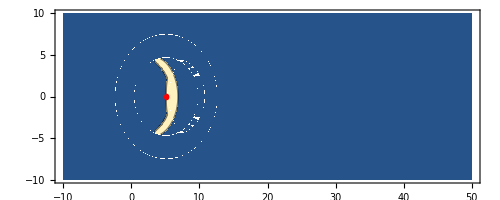

```mathematica
Show[ContourPlot[dphidt[x,y,t],{x,-10,50},{y,-10,10},
Contours->Table[k,{k,0.1,0.1,2}], PlotPoints->40, AspectRatio->Automatic, ContourLabels->False],
Graphics[{Red, Disk[{s[t],0},0.4]}]]
```

```mathematica
Plot3D[dphidt[x,y,12],{x,-10,50},{y,-10,10}]
```

-Graphics3D-